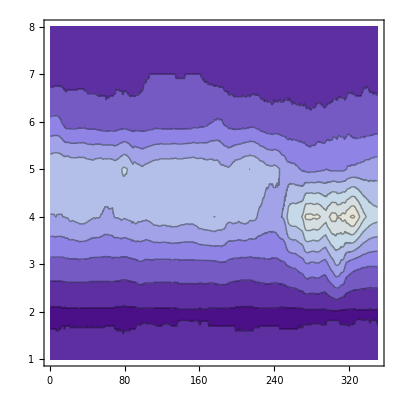

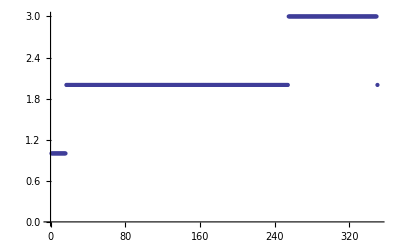

```mathematica
data=(Import["M:\\Proband1\\00506534Schluck7.ASC.data\\data.csv","Data","HeaderLines"->0]);
data2=data[[All,8;;9]];
data3=data[[1;;350,3;;10]];
(*cl = FindClusters[data2,5(*, Method->"Optimize"*)];*)
cl2=ClusteringComponents[data3,3,1,DistanceFunction->EuclideanDistance];
(*,PlotStyle->{{Thick,Red},{Thick,Green}} *)
(*ListPlot[Flatten[cl,0]]*)
ListContourPlot[data3//Transpose]
ListPlot[Flatten[cl2,0]]
```